```mathematica
<<OsculatingOrbitalElements`
```

```mathematica
$UserBaseDirectory
```

/Users/philip/Library/Wolfram

## First, Copy Code for pex version here

### Constants of Motion

```mathematica
Energy[a_?NumericQ, p_?NumericQ, (0|0.), x_?NumericQ] := Energy[a, p, 0, x] =√(((-3+p) (-2+p)^2 p^5
-2 a^5 x (-1+x^2) Sqrt[p^3+a^2 p (-1+x^2)]+a^4 p^2 (-1+x^2) (4-5 p (-1+x^2)+3 p^2 (-1+x^2))-a^6 (-1+x^2)^2 (x^2+p^2 (-1+x^2)-
p (1+2 x^2))+a^2 p^3 (4-4 x^2+p (12-7 x^2)-3 p^3 (-1+x^2)+p^2 (-13+10 x^2))+a (-2 p^(9/2) x Sqrt[p^2+a^2 (-1+x^2)]+4 p^3 x Sqrt[p^3+a^2 p (-1+x^2)])+
2 a^3 (2 p x (-1+x^2) Sqrt[p^3+a^2 p (-1+x^2)]-x^3 Sqrt[p^7+a^2 p^5 (-1+x^2)]))/
((p^2-a^2 (-1+x^2)) ((-3+p)^2 p^4-2 a^2 p^2 (3+2 p-3 x^2+p^2 (-1+x^2))+a^4 (-1+x^2) (-1+x^2+p^2 (-1+x^2)-2 p (1+x^2)))));

Energy[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ]:= Energy[a,p,e,x]=  1/4 √(((-1+e^2)^8 x^4 (-(1/((-1+e^2)^6 x^2))32 a^2 e^2 p^2 (-p^2+a^2 (-1+e^2) (-1+x^2)) 
(-p^3 (-4+3 p+e^2 (4+p))+a^2 (-1+e^2)^2 p^2 (-2+x^2)+a^4 (-1+e^2)^3 (-1+x^2))-32 x 
√(-(1/((-1+e^2)^12 x^8)) a^2 e^4 p^5 (a^4 (-1+e^2)^2+(-4 e^2+(-2+p)^2) p^2+2 a^2 p (-2+p+e^2 (2+p))) (-p^2+a^2 (-1+e^2) (-1+x^2))^3 (p^4-2 a^2 (1+e^2) p^2 
(-1+x^2)+a^4 (-1+e^2)^2 (-1+x^2)^2))+1/((-1+e^2)^8 x^4) 16 e^2 p^2 (p^4 (-3-e^2+p)+a^4 (-1+e^2)^2 (-1+x^2) (-1-x^2+p (-1+x^2)+e^2 (1+x^2))-2 a^2 p^2 
(1+e^4+p (-1+x^2)+e^2 (-2+p (-1+x^2)))) ((-4 e^2+(-2+p)^2) p^3+a^4 (-1+e^2)^2 (-1+x^2) ((-1+e^2) x^2+p (-1+x^2))-a^2 p^2 (4-3 x^2+e^4 x^2+2 p (-1+x^2)
+2 e^2 (-2+x^2+p (-1+x^2))))))/(e^2 p^2 (-4 a^2 (-1+e)^2 (1+e)^2 x^2 (-p^2+a^2 (-1+e^2) (-1+x^2)) (-(3+e^2) p^4+a^2 (-1+e^2)^2 p^2 (-2+x^2)+a^4 (-1+e^2)^3 (-1+x^2))
+((3+e^2-p) p^4-a^4 (-1+e^2)^2 (-1+x^2) (-1-x^2+p (-1+x^2)+e^2 (1+x^2))+2 a^2 p^2 (1+e^4+p (-1+x^2)+e^2 (-2+p (-1+x^2))))^2)));

AngularMomentum[a_?NumericQ, p_?NumericQ, (0|0.), x_?NumericQ]:= AngularMomentum[a,p,0,x]= Module[{En,g,d,h,f},

En = Energy[a,p,0,x];
g=2 a p;
d=(a^2+(-2+p) p) (p^2-a^2 (-1+x^2));
h=((-2+p) p-a^2 (-1+x^2))/x^2;
f=p^4+a^2 (p (2+p)-(a^2+(-2+p) p) (-1+x^2));
(-En g + x Sqrt[(-d h + En^2 (g^2+ f h))/x^2])/h

];

AngularMomentum[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ]:= AngularMomentum[a,p,e,x]= Module[{En},
En = Energy[a,p,e,x];
-(((-1+e) x^2 (2 a En p-x √(1/((-1+e)^6 x^4) (a^2 (-1+e)^2+p (-2+2 e+p)) (-p^2+a^2 (-1+e)^2 (-1+x^2)) (p (-2+2 e+p-En^2 p)+a^2 (-1+e)^2 (-1+En^2) (-1+x^2)))
+e x √(1/((-1+e)^6 x^4) (a^2 (-1+e)^2+p (-2+2 e+p)) (-p^2+a^2 (-1+e)^2 (-1+x^2)) (p (-2+2 e+p-En^2 p)+a^2 (-1+e)^2 (-1+En^2) (-1+x^2)))))
/(-p (-2+2 e+p)+a^2 (-1+e)^2 (-1+x^2)))
]

CarterConstant[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ]:= CarterConstant[a,p,e,x] = (-a^2 (-1+Energy[a,p,e,x]^2)+AngularMomentum[a,p,e,x]^2/x^2) (1-x^2);

AltCarterConstant[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ]:= AltCarterConstant[a,p,e,x]= CarterConstant[a,p,e,x] + (AngularMomentum[a,p,e,x] - a Energy[a,p,e,x])^2; 

R1[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := R1[a,p,e,x] = p/(1-e); 

R2[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := R2[a,p,e,x] = p/(1+e);   

Zm[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := Zm[a,p,e,x] = Sqrt[1-x^2]; 

R3[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := R3[a,p,e,x] = Module[{r1, r2, En, Q},
r1 = R1[a,p,e,x];
r2 = R2[a,p,e,x]; 
En = Energy[a,p,e,x];
Q = CarterConstant[a,p,e,x];
1/(1-En^2) - (r1 + r2)/2 + Sqrt[(-(1/(1-En^2)) + (r1 + r2)/2 )^2 - (a^2 Q)/(r1 r2 (1 - En^2))]
] 

R4[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := R4[a,p,e,x] = Module[{r1, r2,r3, En, Q},
r1 = R1[a,p,e,x];
r2 = R2[a,p,e,x];
r3 = R3[a,p,e,x];
En = Energy[a,p,e,x];
Q = CarterConstant[a,p,e,x];
(a^2  Q)/(r1 r2 r3 (1-En^2)) 
]

Zp[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := Zp[a,p,e,x] = Sqrt[a^2 (1 - Energy[a,p,e,x]^2) + (AngularMomentum[a,p,e,x]^2)/(x^2) ]; 

KR[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := KR[a,p,e,x] = Module[{r1,r2, r3, r4}, 
r1 = R1[a,p,e,x];
r2 = R2[a,p,e,x]; 
r3 = R3[a,p,e,x];
r4 = R4[a,p,e,x];
((r1-r2)(r3-r4))/((r1-r3)(r2-r4))
]; 

KZ[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := KZ[a,p,e,x] = a^2 (1-Energy[a,p,e,x]^2) Zm[a,p,e,x]^2/Zp[a,p,e,x]^2;       

ΥR[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ]:= ΥR[a,p,e,x] = (π Sqrt[(1 - Energy[a,p,e,x]^2)(R1[a,p,e,x] - R3[a,p,e,x])(R2[a,p,e,x] - R4[a,p,e,x])])/(2 EllipticK[KR[a,p,e,x]]);

ΥZ[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := ΥZ[a,p,e,x] = (π Zp[a,p,e,x])/(2EllipticK[KZ[a,p,e,x]] );  


Γ[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ]:= Γ[a,p,e,x]= Module[{M=1,En,L,K,Q, r1,r2,r3,r4,zm,kr,kz, Υr,Υz,rp,rm,hr,hm,hp,a2zp,ϵ0zp},

 En = Energy[a,p,e,x];
 L = AngularMomentum[a,p,e,x];
 zm = Zm[a,p,e,x];
 
 r1 = R1[a,p,e,x];
 r2 = R2[a,p,e,x];
 r3 = R3[a,p,e,x];
 r4 = R4[a,p,e,x]; 
 
 kr = KR[a,p,e,x];
 kz = KZ[a,p,e,x];
 
 Υr = ΥR[a,p,e,x];
 Υz = ΥZ[a,p,e,x];
 
rp=M+Sqrt[M^2-a^2];
rm=M-Sqrt[M^2-a^2];

hr=(r1-r2)/(r1-r3);
hp=((r1-r2)(r3-rp))/((r1-r3)(r2-rp));
hm=((r1-r2)(r3-rm))/((r1-r3)(r2-rm));
 
 
a2zp=(L^2+a^2 (-1+En^2) (-1+zm^2))/( (-1+En^2) (-1+zm^2));

ϵ0zp=-((L^2+a^2 (-1+En^2) (-1+zm^2))/(L^2 (-1+zm^2)));
 
 
 
 

4M^2 En + (2a2zp En  Υz)/(Pi L Sqrt[ϵ0zp]) (EllipticK[kz]- EllipticE[kz]) + 
(2Υr)/(Pi Sqrt[(1-En^2)(r1-r3)(r2-r4)]) (En/2 ((r3(r1+r2+r3)-r1 r2)EllipticK[kr]+
(r2-r3)(r1+r2+r3+r4)EllipticPi[hr,kr]+(r1-r3)(r2-r4)EllipticE[kr])+
2M En(r3 EllipticK[kr]+(r2-r3)EllipticPi[hr,kr])+
(2M)/(rp-rm) (((4M^2 En-a L)rp-2M a^2 En)/(r3-rp) (EllipticK[kr]-(r2-r3)/(r2-rp) EllipticPi[hp,kr])-
((4M^2 En-a L)rm-2M a^2 En)/(r3-rm) (EllipticK[kr]-(r2-r3)/(r2-rm) EllipticPi[hm,kr])))

]

Υϕ[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := Module[{M=1,En,L,K,Q, r1,r2,r3,r4,zm,kr,kz, Υr,Υz,rp,rm,hr,hm,hp,ϵ0zp},

 En = Energy[a,p,e,x];
 L = AngularMomentum[a,p,e,x];
 zm = Zm[a,p,e,x];
 
 r1 = R1[a,p,e,x];
 r2 = R2[a,p,e,x];
 r3 = R3[a,p,e,x];
 r4 = R4[a,p,e,x]; 
 
 kr = KR[a,p,e,x];
 kz = KZ[a,p,e,x];
 
 Υr = ΥR[a,p,e,x];
 Υz = ΥZ[a,p,e,x];
 
rp=M+Sqrt[M^2-a^2];
rm=M-Sqrt[M^2-a^2];

hr=(r1-r2)/(r1-r3);
hp=((r1-r2)(r3-rp))/((r1-r3)(r2-rp));
hm=((r1-r2)(r3-rm))/((r1-r3)(r2-rm));
 
 

ϵ0zp=-((L^2+a^2 (-1+En^2) (-1+zm^2))/(L^2 (-1+zm^2)));
 
 
 
 

(2Υz)/(Pi Sqrt[ϵ0zp]) EllipticPi[zm^2,kz]+
(2a Υr)/(Pi(rp-rm)Sqrt[(1-En^2)(r1-r3)(r2-r4)])((2M En rp - a L)/(r3-rp) (EllipticK[kr]-(r2-r3)/(r2-rp) EllipticPi[hp,kr])-
(2M En rm - a L)/(r3-rm) (EllipticK[kr]-(r2-r3)/(r2-rm) EllipticPi[hm,kr]))

]

ΣAvg[a_?NumericQ, p_?NumericQ, e_?NumericQ, x_?NumericQ] := Module[{M=1,En,L,K,Q, r1,r2,r3,r4,zm,zp,kr,kz,hr},

 En = Energy[a,p,e,x];
 zm = Zm[a,p,e,x];
 zp = Zp[a,p,e,x];
 
 r1 = R1[a,p,e,x];
 r2 = R2[a,p,e,x];
 r3 = R3[a,p,e,x];
 r4 = R4[a,p,e,x]; 
 
 kr = KR[a,p,e,x];
 kz = KZ[a,p,e,x];
 

hr=(r1-r2)/(r1-r3);

 
 1/2 (-((2 zp^2)/(-1+En^2))+r1 (-r2+r3)+r3 (r2+r3))+((r1-r3) (r2-r4) EllipticE[kr])/(2 EllipticK[kr])
 +(zp^2 EllipticE[kz])/((-1+En^2) EllipticK[kz])+((r2-r3) (r1+r2+r3+r4) EllipticPi[hr,kr])/(2 EllipticK[kr])
 

]
```

### Gas Drag Force

```mathematica
KerrGasDragapex[a_, p_, e_, x_, ψr_, ψθ_] := Module[{En,L,Q,ur,uθ,uϕup,utup,ut,uϕ,un,uztup,uzϕup, uzt,at,ar,aθ,aϕ, r1, r2, r, β, zm, zp, z, Σ, Δ, ω,F, θ, P, J }, 

r1 = p/(1 - e);
r2 = p/(1 + e) ;

{En,L,Q} = {Energy[a,p,e,x],AngularMomentum[a,p,e,x],CarterConstant[a,p,e,x]};

(*r coordinate*)
r = p/(1 + e Cos[ψr]) ;
β= a^2 (1 - En^2);

(*Polar Roots*)
zm = 1/(2β) ((L^2+ Q + β) - Sqrt[(L^2 + Q + β)^2 - 4β Q ] ); 
zp = 1/(2β) ((L^2+ Q + β)+ Sqrt[(L^2+ Q + β)^2 - 4β Q] );
z = zm Cos[ψθ]^2;

(*Useful Shorthand*)
Σ = r^2 + a^2 zm Cos[ψθ]^2;
Δ = r^2 + a^2 - 2r;
ω = Sqrt[r^2+ a^2];
F = (r^2+ a^2) En- a L;
θ = ArcCos[Sqrt[zm]Cos[ψθ]];
J = (1-En^2)(1-e^2) + 2(1 - En^2-(1-e^2)/p)(1 + e Cos[ψr]) + ((1 - En^2) (3+ e^2)/(1 - e^2) - 4/p+ (β + L^2 +Q) (1-e^2)/p^2)(1+e Cos[ψr])^2;
P = (p Sqrt[J])/(1 - e^2); 

(*Particle Velocities*)
ur = (p e Sin[ψr] P)/(Δ (1+ e Cos[ψr])^2); 
uθ = (Sqrt[zm]Sin[ψθ])/Sin[θ] Sqrt[β(zp - z)];
uϕup =  1/Σ (L/(1 - zm Cos[ψθ]^2) + a En (ω^2/Δ -1) - (a^2 L)/Δ);
utup = 1/Σ (En(ω^4/Δ - a^2 (1 - zm Cos[ψθ]^2)) + a L (1 - ω^2/Δ)); 
ut = -(1 - (2r)/Σ)utup -(2 a r(1-zm Cos[ψθ]^2))/Σ uϕup; 
uϕ = -((2 a r(1-zm Cos[ψθ]^2))/Σ)utup + ((ω^4 -Δ a^2 (1-zm Cos[ψθ]^2))(1-zm Cos[ψθ]^2))/Σ uϕup ;   
un = -(F /(2Σ))- Δ/(2Σ) ur; 

(*ZAMO Velocities*)
uztup =  Sqrt[(ω^4- Δ a^2 (1-zm Cos[ψθ]^2))/(Σ Δ )]; 
uzϕup = (2 a r)/Sqrt[Σ Δ (ω^4- Δ a^2 (1-zm Cos[ψθ]^2))];  
uzt = -(1 - (2 r)/Σ) uztup  - (2 a r(1-zm Cos[ψθ]^2))/Σ uzϕup; 
(*Gas Drag*)

at = -(ut + uzt/(uzt utup));
ar = -(ur);
aθ = -(uθ);
aϕ = -(uϕ);

<|"at" -> at, "ar" -> ar, "aθ" -> aθ, "aϕ" ->   aϕ|>
]
```

### Generic Kerr Oosculating Geodesics (apex)

```mathematica
GenericKerrpexBL[BHparams_,ICs_, tmax_,pmin_,opts:OptionsPattern[]]:= Module[{ initialConditions, EoM,η,a,p0,e0,x0,ψr0,ψθ0,ϕ0,p,e,x,ψr,ψθ, ϕ,t, λ, En, L,Q,K,r1,r2,r,β,zm,βzp,z,Σ,Σ1,Σ2, Δ,Δ1,Δ2,ω,ω1,ω2,F,F1,F2,
H,θ,κ1,κ2,Q1,Q2,C,𝒟,ϵ,J,P,G,ur,uθ,un,utup,uZAMOtup,uZAMOϕup,uZAMOt, at,ar,aθ,aϕ,dEdλ,dLdλ,dKdλ,dr1dλ,dr2dλ,dpdλ,dedλ,dzmdλ,dxdλ,A1,A2,A3,an,dtdλ,dϕdλ,dψrdλ,dψθdλ,psol, esol, xsol, 
ψrsol, ψθsol, tsol, ϕsol, progress = 0,rsol,θsol,Ensol,Lsol,Ksol,Qsol,r1sol,r2sol,zmsol,ιsol,uϕup,qr,qz, urup, uθup, 
Ft,Fr,Fθ,Fϕ, σ, Υtsol,Υrsol,Υzsol,Υϕsol,m1,m2,atup,arup,aθup,aϕup,A4,qrsol,qzsol},

{η,a} = BHparams;
{p0,e0,x0} = ICs;
{ψr0,ψθ0,ϕ0} = {0,0,0};

m1 = 1;
m2 = η;

initialConditions = {
p[0] == p0,
e[0]== e0,
x[0] == x0,
ψr[0] == ψr0,
ψθ[0] == ψθ0,
ϕ[0] == ϕ0
}; 

(*roots*)
{En, L, Q} = {Energy[a,p[λ],e[λ],x[λ]],AngularMomentum[a,p[λ],e[λ],x[λ]],CarterConstant[a,p[λ],e[λ],x[λ]]}; 

K = Q +(L-a En)^2;
r1 = p[λ]/(1-e[λ]); 
r2 = p[λ]/(1+e[λ]); 
(*r coordinate*)
r = p[λ]/(1 + e[λ] Cos[ψr[λ]]);
β= a^2 (1 - En^2);
(*Polar Roots*)
(*zm = 1/(2β) ((L^2+ Q + β) - Sqrt[(L^2 + Q + β)^2 - 4β Q ] );*) 
zm = (1-x[λ]^2);
(*zp = 1/(2β) ((L^2+ Q + β)+ Sqrt[(L^2+ Q + β)^2 - 4β Q] );*)
βzp = (a^2(1-En^2)+ L^2/(1-zm));
z = zm Cos[ψθ[λ]]^2;

(*Useful Shorthand*)

Σ = r^2 + a^2 zm Cos[ψθ[λ]]^2;
Σ1 = r1^2 + a^2 zm Cos[ψθ[λ]]^2;
Σ2 = r2^2 + a^2 zm Cos[ψθ[λ]]^2;

Δ = r^2 + a^2 - 2r;
Δ1 = r1^2 + a^2 - 2r1;
Δ2 = r2^2 + a^2 - 2r2;

ω = Sqrt[r^2+ a^2];
ω1 = Sqrt[r1^2+ a^2];
ω2 = Sqrt[r2^2+ a^2];
 
F = (r^2+ a^2) En- a L;
F1 = (r1^2+ a^2) En- a L;
F2 = (r2^2+ a^2) En- a L;

H = L - a En x[λ]^2; (*Fixed Bug that Lisa found*)
θ = ArcCos[Sqrt[zm]Cos[ψθ[λ]]];

κ1 = 4En F1 r1 - 2 r1 Δ1 - 2(r1-1)(r1^2 + K);
κ2 = 4En F2 r2 - 2 r2 Δ2 - 2(r2-1)(r2^2 + K);

Q1 = - 2 a L r r1 - a^4 En(r+r1) + a^3 L(r+r1) - a^2 En(r^3 + r^2 r1 + r1^3 + r r1(-2 + r1)) - En r r1 ( r r1 (r + r1) - 2(r^2 + r r1 + r1^2)) - a^2 (2a^2 En - 2En r r1 + a L(-2 + r + r1)) zm Cos[ψθ[λ]]^2;

Q2 = - 2 a L r r2 - a^4 En(r+r2) + a^3 L(r+r2) - a^2 En(r^3 + r^2 r2 + r2^3 + r r2(-2 + r2)) - En r r2 ( r r2 (r + r2) - 2(r^2 + r r2+ r2^2)) - a^2 (2a^2 En - 2En r r2 + a L(-2 + r + r2)) zm Cos[ψθ[λ]]^2;
C = (Q1 (1- e[λ]))/κ1 - (Q2 (1+ e[λ]))/κ2; 

𝒟 = (1-e[λ])^2 (1 - Cos[ψr[λ]]) Δ1/κ1 + (1+e[λ])^2 (1 + Cos[ψr[λ]]) Δ2/κ2;

ϵ = (F1(1-e[λ])(r+r1))/κ1 - (F2 (1+ e[λ]) (r + r2))/κ2;  
J = (1-En^2)(1-e[λ]^2) + 2(1 - En^2-(1-e[λ]^2)/p[λ])(1 + e[λ] Cos[ψr[λ]]) + ((1 - En^2) (3+ e[λ]^2)/(1 - e[λ]^2) - 4/p[λ]+ (β + L^2 +Q) (1-e[λ]^2)/p[λ]^2)(1+e[λ] Cos[ψr[λ]])^2;
P = (p[λ] Sqrt[J])/(1 - e[λ]^2); 
G =  (ω^2 L)/Sin[θ] - a^3 (1 - zm) Sin[θ] En;



(*Particle Velocities*)
ur = (p[λ] e[λ] Sin[ψr[λ]] P)/(Δ (1+ e[λ] Cos[ψr[λ]])^2); 
urup = Δ/Σ ur;
uθ = (Sqrt[zm]Sin[ψθ[λ]])/Sin[θ] Sqrt[βzp - β z];
uθup = uθ/Σ;
un = -(F /(2Σ))- Δ/(2Σ) ur; 

(*Force Model*)

{at,ar,aθ, aϕ} = η Values[KerrGasDragapex[a, p[λ], e[λ], x[λ], ψr[λ], ψθ[λ]] ];


(*Orbital Element Evolution*)
dEdλ = -Σ at;
dLdλ = Σ aϕ; 
dKdλ = (2Σ)/Δ(-at(ω^4 En - a ω^2 L) + aϕ (a^2 L -a ω^2 En) - Δ^2 ur ar);  

dr1dλ = -2 F1/κ1(ω1^2 dEdλ - a dLdλ) + Δ1/κ1 dKdλ;  
dr2dλ = -2 F2/κ2(ω2^2 dEdλ - a dLdλ) + Δ2/κ2 dKdλ;  

dpdλ = (2 r2^2)/(r1+r2)^2 dr1dλ + (2 r1^2)/(r1+r2)^2 dr2dλ;
dedλ = (2 r2)/(r1+r2)^2 dr1dλ -(2 r1)/(r1+r2)^2 dr2dλ;


(*Convert from BL to Null Tetrad Componets*)

an = ω^2/(2Σ)  at - Δ/(2Σ) ar + a/(2Σ) aϕ;

A1 = aθ;
A2 = -a Sin[θ] at - 1/Sin[θ] aϕ;
A3 = (a(L - a En Sin[θ]^2))/Σ  at + uθ/Σ aθ + (L - a En Sin[θ]^2)/(Σ Sin[θ]^2) aϕ ; 
(*A4 = If[zm == 0.,0.,aθ/(√zm)]; *)(*This is here to get rid of numerical divergence in dϕθdλ*)
(*Valid so long as aθ -> 0 as x -> +-1*)

dtdλ = En(ω^4/Δ - a^2 (1 - zm Cos[ψθ[λ]]^2)) + a L(1 - ω^2/Δ);
dϕdλ = L/(1-zm Cos[ψθ[λ]]^2) + a En (ω^2/Δ-1) - (a^2 L)/Δ;
(*Osculating Geodesic Equations*)
(*Using simpler equations for the evolution of E, L and K*)


dψrdλ = P  +(C A3 Sin[ψr[λ]])/(2(1 + e[λ] Cos[ψr[λ]]) un) + (𝒟 Σ A3 P )/(2(1+ e[λ] Cos[ψr[λ]])^2 un) - (a ϵ Sin[θ]Sin[ψr[λ]] A2)/(1 + e[λ] Cos[ψr[λ]])  +  (P an)/(un ( 1 + e[λ] Cos[ψr[λ]])^2) ((1-e[λ])^2 (1 - Cos[ψr[λ]]) ( Σ1 F1)/κ1  +(1+e[λ])^2 (1+Cos[ψr[λ]]) (Σ2 F2)/κ2);

dψθdλ = Sqrt[βzp - β z]( 1 + ((1 - zm) Σ A1 Cos[ψθ[λ]])/(√zm(βzp - β zm) Sin[θ])) + (Cos[ψθ[λ]] Sin[ψθ[λ]] H a Δ ( A3 - 2 ur an))/(2(βzp -β zm)  un) + (Cos[ψθ[λ]] Sin[ψθ[λ]] G A2 )/((βzp - β zm));

dtdλ = En(ω^4/Δ - a^2 (1 - zm Cos[ψθ[λ]]^2)) + a L(1 - ω^2/Δ);
dϕdλ = L/(1-zm Cos[ψθ[λ]]^2) + a En (ω^2/Δ-1) - (a^2 L)/Δ;

dzmdλ = 1/(βzp - β zm)((1-zm)dKdλ - 2(L - a(1-zm)En)(dLdλ - a (1-zm)dEdλ));  
dxdλ = -1/(2x[λ])dzmdλ;
(*For to check that everything is defined, output the following*)   
(*{dpdλ, dedλ, dxdλ, dψrdλ,dψθdλ,dtdλ dϕdλ}/. {p[λ]-> p0, e[λ]-> e0, x[λ]-> x0, ψr[λ]-> 0, ψθ[λ]-> 0}*)

EoM ={
p'[λ] == dpdλ/dtdλ,
e'[λ] == dedλ/dtdλ,
x'[λ] == dxdλ/dtdλ,
ψr'[λ] == dψrdλ/dtdλ,
ψθ'[λ] == dψθdλ/dtdλ,
ϕ'[λ] == dϕdλ/dtdλ
};

{{psol, esol, xsol, ψrsol, ψθsol, ϕsol}} = Monitor[{p, e, x, ψr, ψθ, ϕ} /. NDSolve[{Join[EoM, initialConditions],WhenEvent[p[λ] - pmin == 0, "StopIntegration"]}, {p,e,x,ψr,ψθ, ϕ}, 
	{λ,0,tmax}, FilterRules[{opts},Options[NDSolve]], StepMonitor :> (progress = λ)],  "t = "<> ToString[progress]];
	
(*Define the evolution of other quantities of interest*)
zmsol[λ_]:= 1 - xsol[λ]^2;
rsol[λ_] := psol[λ]/(1 + esol[λ] Cos[ψrsol[λ]]); 
θsol[λ_] :=  ArcCos[Sqrt[zmsol[λ]]Cos[ψθsol[λ]]];
Ensol[λ_] := Energy[a,psol[λ],esol[λ],xsol[λ]];
Lsol[λ_] := AngularMomentum[a,psol[λ],esol[λ],xsol[λ]]; 
Qsol[λ_] := CarterConstant[a,psol[λ],esol[λ],xsol[λ]];
Ksol[λ_] := Qsol[λ] + (Lsol[λ] - a Ensol[λ])^2;
r1sol[λ_]:= psol[λ]/(1-esol[λ]);
r2sol[λ_]:= psol[λ]/(1+esol[λ]); 
ιsol[λ_] := ArcCos[Lsol[λ]/Sqrt[Ksol[λ] + 2 a Lsol[λ] Ensol[λ] - a^2 Ensol[λ]^2]];

Υtsol[λ_]:= Γ[a,psol[λ], esol[λ], xsol[λ]];
Υrsol[λ_]:= ΥR[a,psol[λ], esol[λ], xsol[λ]];
Υzsol[λ_]:= ΥZ[a,psol[λ], esol[λ], xsol[λ]];
Υϕsol[λ_]:= Υϕ[a,psol[λ], esol[λ], xsol[λ]];

(*qrsol[λ_]:= qrConv[a,psol[λ],esol[λ],xsol[λ],ψrsol[λ]];
qzsol[λ_]:= qzConv[a,psol[λ],esol[λ],xsol[λ],ψθsol[λ]];*)

(*Retrun the results*)
<| "r" -> rsol, "θ" -> θsol, "ϕ"-> ϕsol, 
"En"-> Ensol, "L"-> Lsol, "K" -> Ksol, "Q" -> Qsol, 
"p"-> psol, "e"-> esol, "x" -> xsol, "ι" -> ιsol,
"ψr" -> ψrsol, "ψθ" -> ψθsol,(*"qr" -> qrsol, "qz" -> qzsol,*)
 "r1"-> r1sol, "r2" -> r2sol, "z1"-> zmsol, 
 "Υt" -> Υrsol, "Υr" -> Υrsol,"Υz" -> Υzsol,"Υϕ" -> Υϕsol,
"r"-> rsol, "θ"-> θsol, "ϕ"-> ϕsol,
 "limit" -> psol["Domain"][[1,2]]|>

]
```

## Then test against package (should be just as accurate, maybe faster)

```mathematica
ηtest = 10^-3;
atest = 0.3;
ptest = 40;
etest = 0.1;
xtest = 0.5;
```

```mathematica
AbsoluteTiming[pex = GenericKerrpexBL[{ηtest,atest},{ptest,etest,xtest}, 10^6,2,{AccuracyGoal-> 13, PrecisionGoal-> 13}]]
```

NDSolve::ndsz: At λ$1766023 == 712.125, step size is effectively zero; singularity or stiff system suspected.

{1.08124,<|r→rsol$1766023,θ→θsol$1766023,ϕ→InterpolatingFunction[…],En→Ensol$1766023,L→Lsol$1766023,K→Ksol$1766023,Q→Qsol$1766023,p→InterpolatingFunction[…],e→InterpolatingFunction[…],x→InterpolatingFunction[…],ι→ιsol$1766023,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→r1sol$1766023,r2→r2sol$1766023,z1→zmsol$1766023,Υt→Υrsol$1766023,Υr→Υrsol$1766023,Υz→Υzsol$1766023,Υϕ→Υϕsol$1766023,limit→712.125|>}

```mathematica
AbsoluteTiming[ELK =KerrOsculatingOrbitalElementsTP[ηtest, atest, ptest, etest,xtest, 0, 0 , AccuracyGoal->10, PrecisionGoal->10] ]
```

Starting NDSolve...

Unbound orbit encountered.

{19.3238,<|r→OsculatingOrbitalElements`Private`rsol$1771837,θ→OsculatingOrbitalElements`Private`θsol$1771837,ϕ→InterpolatingFunction[…],En→InterpolatingFunction[…],L→InterpolatingFunction[…],K→InterpolatingFunction[…],Q→OsculatingOrbitalElements`Private`Qsol$1771837,p→OsculatingOrbitalElements`Private`psol$1771837,e→OsculatingOrbitalElements`Private`esol$1771837,x→OsculatingOrbitalElements`Private`xsol$1771837,ι→OsculatingOrbitalElements`Private`ιsol$1771837,ψr→InterpolatingFunction[…],ψθ→InterpolatingFunction[…],r1→OsculatingOrbitalElements`Private`r1sol$1771837,r2→OsculatingOrbitalElements`Private`r2sol$1771837,z1→OsculatingOrbitalElements`Private`zmsol$1771837,limit→712.125|>}

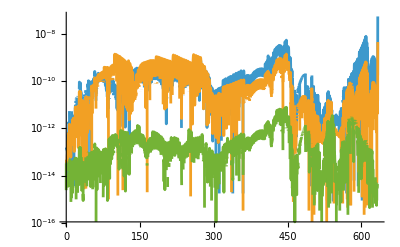

```mathematica
LogPlot[{Abs[pex["p"][t]- ELK["p"][t]],{Abs[pex["e"][t]- ELK["e"][t]]},{Abs[pex["x"][t]- ELK["x"][t]]}},{t,0,pex["limit"]}]
```

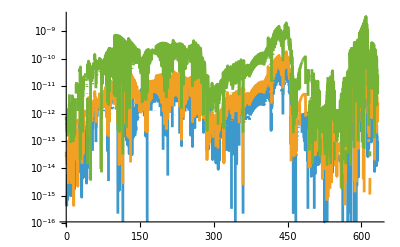

```mathematica
LogPlot[{Abs[pex["En"][t]- ELK["En"][t]],{Abs[pex["L"][t]- ELK["L"][t]]},{Abs[pex["K"][t]- ELK["K"][t]]}},{t,0,pex["limit"]}]
```

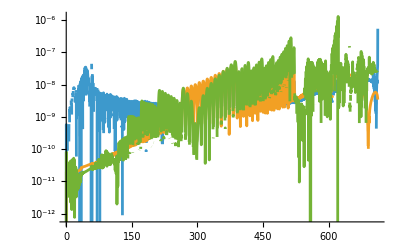

```mathematica
LogPlot[{Abs[pex["ψr"][t]- ELK["ψr"][t]],{Abs[pex["ψθ"][t]- ELK["ψθ"][t]]},{Abs[pex["ϕ"][t]- ELK["ϕ"][t]]}},{t,0,pex["limit"]}]
```

```mathematica
LogPlot[{Abs[pex["En"][t]- ELK["En"][t]],{Abs[pex["L"][t]- ELK["L"][t]]},{Abs[pex["K"][t]- ELK["K"][t]]}},{t,0,pex["limit"]}]
```

-Graphics-

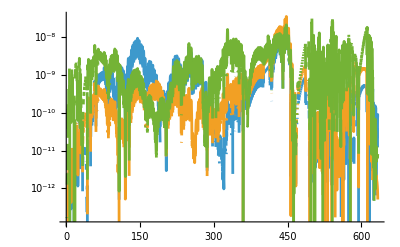

```mathematica
LogPlot[{Abs[pex["ψr"][t]- ELK["ψr"][t]],{Abs[pex["ψθ"][t]- ELK["ψθ"][t]]},{Abs[pex["ϕ"][t]- ELK["ϕ"][t]]}},{t,0,pex["limit"]}]
```